Monte-Carlo Methods. 

Monte-Carlo Method-1

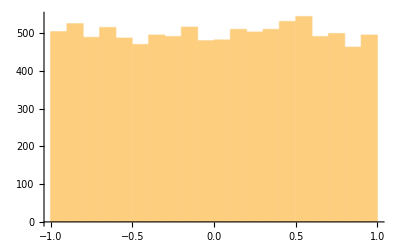

```mathematica
alist=Histogram[Table[2(RandomReal[]-0.5),{i,1,10000}]]
```

```mathematica
Clear["Global`*"]
```

```mathematica
data=Table[alist=Table[2(RandomReal[]-0.5),{i,1,Nmat}];
blist=Table[2(RandomReal[]-0.5),{i,1,Nmat}];
clist=Table[2(RandomReal[]-0.5),{i,1,Nmat}];
dlist=Table[2(RandomReal[]-0.5),{i,1,Nmat}];
taulist=alist+dlist;
deltalist=alist dlist-blist clist;
disclist=taulist taulist-4 deltalist;
fracsaddle=Total[(1-UnitStep[deltalist])/Length[deltalist]]//N;
fracunstablenodes=Total[(UnitStep[taulist]UnitStep[disclist]UnitStep[deltalist])/Length[taulist]]//N;
{Nmat,fracsaddle,fracunstablenodes},{Nmat,100000,1000000,100000}]
```

{{100000,0.49971,0.09078},{200000,0.500055,0.090715},{300000,0.499593,0.0901067},{400000,0.500105,0.090605},{500000,0.500618,0.089622},{600000,0.500095,0.0903667},{700000,0.500647,0.0899943},{800000,0.499738,0.0906063},{900000,0.499903,0.0900667},{1000000,0.500125,0.090275}}

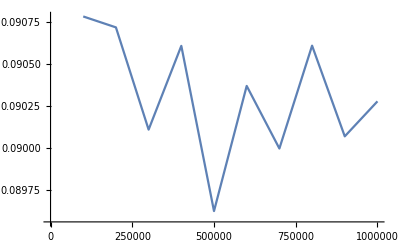

```mathematica
ListLinePlot[data[[All,{1,3}]]]
```

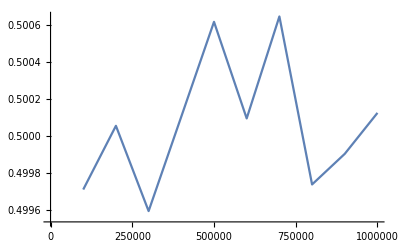

```mathematica
ListLinePlot[data[[All,{1,2}]]]
```

Monte-Carlo Method-2

```mathematica
Clear["Global`*"]
```

```mathematica
app=Table[n=2^k;{n,Mean[Table[Mean[Table[1/(RandomReal[]+1),{n}]],{1000}]]},{k,5,10}]
```

{{32,0.693746},{64,0.692686},{128,0.693269},{256,0.693578},{512,0.693226},{1024,0.692939}}

```mathematica
TableForm[app]
```

32 | 0.693746
64 | 0.692686
128 | 0.693269
256 | 0.693578
512 | 0.693226
1024 | 0.692939

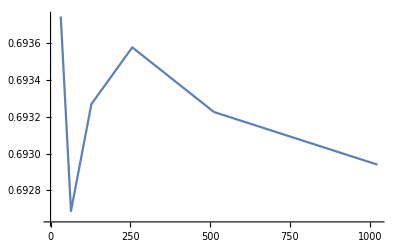

```mathematica
ListPlot[app,Joined->True]
```

```mathematica
errapp=Table[n=2^k;{n,Mean[Table[Abs[Mean[Table[1/(RandomReal[]+1),{n}]-Log[2]]],{1000}]]},{k,5,10}]
```

{{32,0.0200387},{64,0.0143177},{128,0.00953119},{256,0.0069096},{512,0.00493057},{1024,0.00341155}}

```mathematica
TableForm[errapp]
```

32 | 0.0200387
64 | 0.0143177
128 | 0.00953119
256 | 0.0069096
512 | 0.00493057
1024 | 0.00341155

```mathematica
fn[x_]=c x^d;
fit=FindFit[errapp,{c x^d},{c,d},{x}]
```

{c→0.119399,d→-0.514224}

```mathematica
g[x_]=fn[x]/.fit
```

0.119399/x^0.514224

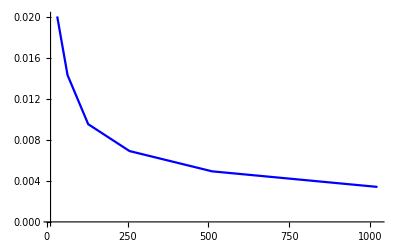

```mathematica
ListPlot[errapp,Joined->True,PlotStyle->Blue,PlotRange->Full]
```

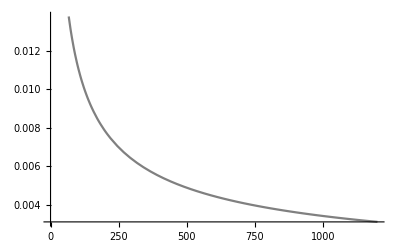

```mathematica
Plot[g[x],{x,0,1200},PlotStyle->Gray]
```

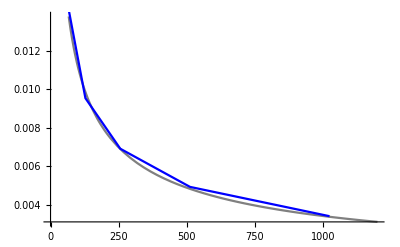

```mathematica
Show[Plot[g[x],{x,0,1200},PlotStyle->Gray],ListPlot[errapp,Joined->True,PlotStyle->Blue,PlotRange->Full]]
```

```mathematica
Clear["Global`*"]
```

```mathematica
data = Table[n = 2^k; {n, Mean[Table[Mean[Table[4/(RandomReal[]^2 + 1), {n}]], {1000}]]}, {k,5,10}];
```

```mathematica
TableForm[data]
```

32 | 3.14032
64 | 3.14275
128 | 3.13921
256 | 3.13927
512 | 3.1421
1024 | 3.14104

```mathematica
app1=Table[n=2^k;{n,Mean[Table[Mean[Table[4/(RandomReal[]^2+1),{n}]],{1000}]]},{k,5,10}]
```

{{32,3.13357},{64,3.14369},{128,3.14304},{256,3.1384},{512,3.1425},{1024,3.14142}}

```mathematica
TableForm[app1]
```

32 | 3.13357
64 | 3.14369
128 | 3.14304
256 | 3.1384
512 | 3.1425
1024 | 3.14142

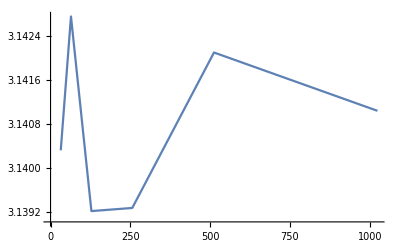

```mathematica
ListPlot[data,Joined->True]
```

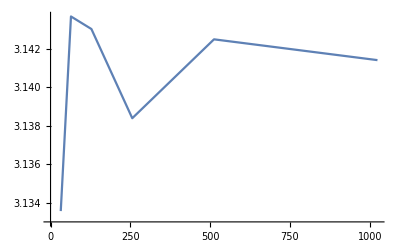

```mathematica
ListPlot[app1,Joined->True]
```

```mathematica
errapp1=Table[n=2^k;{n,Mean[Table[Abs[Mean[Table[4/(RandomReal[]^2+1),{n}]-π]],{1000}]]},{k,5,10}]
```

{{32,0.0913473},{64,0.0645263},{128,0.0431631},{256,0.0320078},{512,0.0223982},{1024,0.0159606}}

```mathematica
TableForm[errapp1]
```

32 | 0.0913473
64 | 0.0645263
128 | 0.0431631
256 | 0.0320078
512 | 0.0223982
1024 | 0.0159606

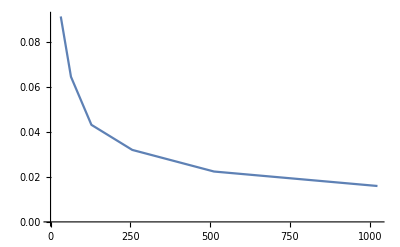

```mathematica
ListPlot[errapp1,Joined->True]
```

```mathematica
gn[x_]=a x^b;
fit1=FindFit[errapp1,{a x^b},{a,b},{x}]
```

{a→0.537996,b→-0.511972}

```mathematica
gn[x]/.fit1
```

0.537996/x^0.511972

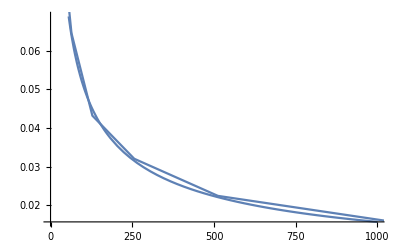

```mathematica
Show[Plot[gn[x]/.fit1,{x,0,1000}],ListPlot[errapp1,Joined->True]]
```

Monte-Carlo Method-3

```mathematica
p[x_]:=Exp[1-x]/(ⅇ-1)
Dist=ProbabilityDistribution[p[x],{x,0,1}];
PDF[Dist,x]
```

Piecewise[{{ⅇ^(1-x)/(-1+ⅇ), 0<x<1}, {0, True}}]

```mathematica
PiecewiseExpand[Piecewise[{{ⅇ^(1-x)/(-1+ⅇ),0<x<1}},0]]
```

Piecewise[{{ⅇ^(1-x)/(-1+ⅇ), 0<x<1}, {0, True}}]

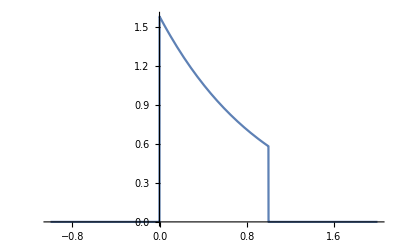

```mathematica
Plot[PDF[Dist,x],{x,-1,2}]
```

```mathematica
f[x_]=4/(1+x^2);
```

```mathematica
RandomVariate[Dist, 10];
```

```mathematica
Histogram[RandomVariate[Dist, 1000]];
```

```mathematica
Table[xi=RandomVariate[Dist];f[xi]/p[xi],{100}];
```

```mathematica
data1=Table[n=2^k;{n,Mean[Table[Mean[Table[xi=RandomVariate[Dist];f[xi]/p[xi],{n}]],{1}]]},{k,5,10}]
```

{{32,3.12965},{64,3.17525},{128,3.16335},{256,3.15403},{512,3.1279},{1024,3.14676}}

```mathematica
TableForm[data1]
```

32 | 3.12965
64 | 3.17525
128 | 3.16335
256 | 3.15403
512 | 3.1279
1024 | 3.14676

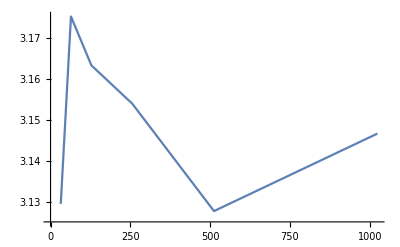

```mathematica
ListPlot[data1,Joined->True]
```

```mathematica
errdata1=Table[n=2^k;{n,Mean[Table[Abs[Mean[Table[xi=RandomVariate[Dist];f[xi]/p[xi],{n}]-π]],{1}]]},{k,5,10}]
```

{{32,0.0685127},{64,0.0122823},{128,0.0145376},{256,0.0111463},{512,0.00952744},{1024,0.00129849}}

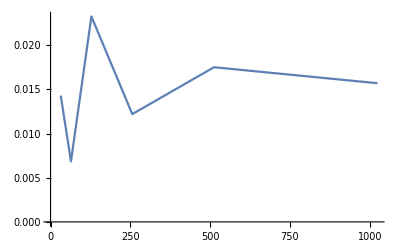

```mathematica
ListPlot[errdata1,Joined->True]
```

```mathematica
k[x_]=r x^q;
fit2=FindFit[errdata1,{r x^q},{r,q},{x}]
```

{r→21.2559,q→-1.66242}

```mathematica
h[x_]=k[x]/.fit2
```

21.2559/x^1.66242

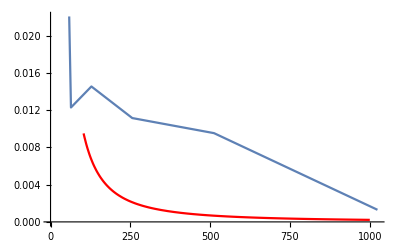

```mathematica
Show[ListPlot[errdata1,Joined->True],Plot[h[x],{x,0,1000},PlotStyle->Red]]
```

Monte-Carlo 4

```mathematica
Clear["Global`*"]
```

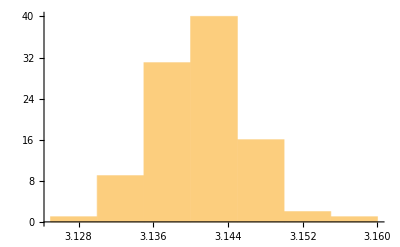

```mathematica
set=Table[nMax=100000;1/nMax(Table[If[(RandomReal[{0,1},2]^2//Total)<=1,1,0],nMax]//Total)4.0,{100}];
Histogram[set]
```

```mathematica
Mean[set]
```

3.14084